## 105A Final Exam 2012

40 points + 5 point bonus. Do all problems, show all work. Open book, open notes test. 
You may use a web browser only to visit the class web site. If a problem does not specify a method of solution, you may use any method. The “by hand” method means to use pen/pencil and paper.

Problem 1 (10 points)

(a) Find numerical values for all real solutions for x to the following equation, using Mathematica : x^8- 4 x + 3 = 0.

(b) Find, by hand, the Fourier transform of t e^-t h(t) where h(t) is the Heaviside step function.

(c) Use Fourier transform methods to find a particular solution to the following 2nd-order differential equation:

			ϕ''(t)+4ϕ'(t)+5ϕ(t)= t e^-t h(t).

You may use Mathematica to help perform the transform and inverse transform, if you wish.

### Solution

#### (a)

```mathematica
Solve[x^8 - 4 x + 3 ==0,x]//N
```

{{x→1.},{x→0.786666},{x→-1.18092-0.536729 ⅈ},{x→-1.18092+0.536729 ⅈ},{x→-0.360693-1.21303 ⅈ},{x→-0.360693+1.21303 ⅈ},{x→0.648284-0.997426 ⅈ},{x→0.648284+0.997426 ⅈ}}

The first two solutions are real. Or, you can plot the function and use findroot

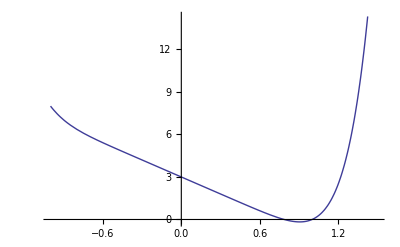

```mathematica
Plot[x^8 - 4 x + 3 ,{x,-1,3/2}]
```

```mathematica
FindRoot[x^8 - 4 x + 3==0,{x,.6}]
```

{x→0.786666}

```mathematica
FindRoot[x^8 - 4 x + 3==0,{x,1}]
```

{x→1.}

#### (b)

∫_(-∞)^∞ ⅆt ⅇ^(ⅈ ω t)t  e^-t h(t) =1/ⅈ∂/(∂ω)∫_0^∞ ⅆt ⅇ^(ⅈ ω t)  e^-t=1/ⅈ∂/(∂ω)∫_0^∞ ⅆt ⅇ^(-(1-i ω)t)=1/ⅈ∂/(∂ω)1/(1-ⅈ ω)=1/(1-ⅈ ω)^2.

Check:

```mathematica
FourierTransform[t Exp[-t] UnitStep[t],t,ω] Sqrt[2Pi]//Expand
```

-1/(ⅈ+ω)^2

#### (c)

The  lhs has a Fourier transform (5-4 ⅈ ω-5 ω^2 )ϕ̃(ω). So the particular solution is

```mathematica
ϕp[t_] = InverseFourierTransform[%/(5-4 ⅈ ω-ω^2 ),ω,t]/Sqrt[2Pi]//Simplify
```

1/4 ⅇ^((-2-ⅈ) t) (1+ⅇ^(2 ⅈ t)+2 ⅇ^((1+ⅈ) t) (-1+t)) HeavisideTheta[t]

This could be simplified to 1/2( ⅇ^(-2 t) cos t+ⅇ^-t (-1+t)) h(t).

Problem 2 (10 pts)

Using separation of variable , find and plot as a surface plot the potential ϕ(x,y) inside the following rectangular enclosure, with the given boundary conditions. The potential satsifies Laplace’s equation.  For the plot take a=2, b=1.

### Solution

The solution that matches the boundary conditions on the top, bottom and right has the form 
			ϕ(x,y) = ∑_(n=0,1,...) A_n cos((n+1/2) π y/b)sinh((n+1/2) π x/b)].
[Can be found via separation of variables: ϕ(x,y) = X(x) Y(y),  which when used in Laplaces equation implies X''=k^2 X,Y''=-k^2Y . Homogeneous Neumann boundary conditions on the Y equation imply it is an eigenvalue problem with the solution  Y=cos k y, k=(n+1/2) π/b. General solution of the X equation is X=A ⅇ^(k x) + B ⅇ^(-k x). The solution that matches the right side is X=A sinh(k x) ].

```mathematica
Clear["Global`*"]
```

```mathematica
A[n_] = Integrate[y^2(y-b)^2 Cos[(n+1/2) Pi y/b],{y,0,b}] 2/(b Sinh[(n+1/2) Pi a/b])
```

-(32 b^4 Csch[(a (1/2+n) π)/b] ((-48+(π+2 n π)^2) Cos[n π]-12 (1+2 n) π (-1+Sin[n π])))/(π+2 n π)^5

```mathematica
ϕ[x_,y_] = Sum[A[n] Cos[(n+1/2) Pi y/b] Sinh[(n+1/2) Pi x/b],{n,0,10}];
```

```mathematica
a=2;b=1;
```

```mathematica
Plot3D[ϕ[x,y],{x,0,a},{y,0,b},AspectRatio->Automatic,PlotRange->All,PlotPoints->30,Mesh->False,BoxRatios->{1.5,1,1/2},AxesLabel->{"x","y","ϕ"}]
```

-Graphics3D-

Check to ensure we are matching the boundary condition at x=a:

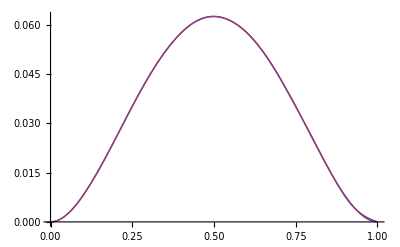

```mathematica
Plot[Evaluate[{ϕ[a,y],y^2(y-b)^2}],{y,0,1}]
```

Problem 3 (10 pts)

Using separation of variables, find the solution for T(r,t) on 0≤ r≤ 1 to the following heat equation problem in cylindrical coordinates:

			(∂T)/(∂t)=1/r∂/(∂r)(r(∂T)/(∂r))+9r,    T(1,t)=0,   with initial condition T(r,0)=0. 

   Plot the solution at t=0.1, and find T(1/2,0.1) .

### Solution

Equilibrium: 1/r∂/(∂r)(r(∂T_eq)/(∂r))+9r=0,  with boundary conditions T_eq(1)=0. The solution is
T_eq(r) =1-r^3, found by direct integration or using DSolve.

```mathematica
Clear["Global`*"]
```

```mathematica
Teq[r_] = 1-r^3;
```

deviation from equilibrium:
Initial condition on ΔT is ΔT(x,0)=0-T_eq(r).
Use separation of variable to write ΔT as ΔT=f(t)ψ(r) where eigenmodes ψ(r) satisfy 
1/r∂/(∂r)(r(∂ψ)/(∂r))=-k^2ψ, ψ(1)=0.
 The eigenmodes that satisfy the boundary conditions are J_0(k r), with k=j_(0n).

Separation implies f'(t) =-k^2f(t)  

so f=A_nExp[-k^2 t].

```mathematica
ψ[n_,r_] = BesselJ[0,j[n] r];
```

```mathematica
j[n_] := (j[n]=N[BesselJZero[0,n]])/; n∈Integers
```

```mathematica
A[n_] = Integrate[ψ[n,r](-Teq[r])r,{r,0,1}]/Integrate[ψ[n,r]^2r,{r,0,1}]
```

(9 BesselJ[1,j[n]] (-2 j[n]+π StruveH[0,j[n]])+3 BesselJ[0,j[n]] (2 j[n]^2-3 π StruveH[1,j[n]]))/((BesselJ[0,j[n]]^2+BesselJ[1,j[n]]^2) j[n]^4)

```mathematica
ΔT[r_,t_] = Sum[A[n]Exp[-j[n]^2 t] ψ[n,r],{n,1,10}] ;
```

```mathematica
T[r_,t_] = Teq[r] + ΔT[r,t];
```

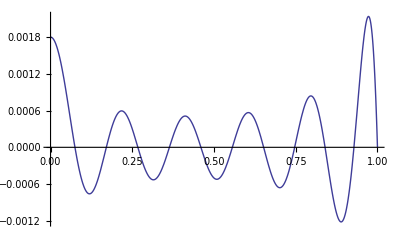

```mathematica
Plot[T[r,0],{r,0,1}]
```

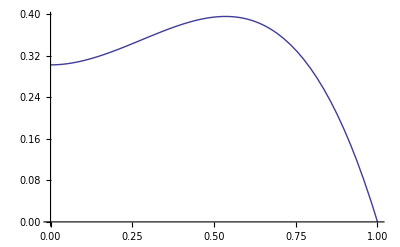

```mathematica
Plot[T[r,0.1],{r,0,1},PlotRange->All]
```

```mathematica
Table[Plot[T[r,t],{r,0,1},PlotRange->{0,1},PlotLabel->"t = "<>ToString[N[t,2]]],{t,0,1,.02}];
ListAnimate[%]
```

```mathematica
T[.5,.1]
```

1.31452

Problem 4 (10 pts + 5 pt Bonus)

(a) Find a Greens function for the following  differential equation on the range 0≤t,  and use it to obtain and plot the solution on 0<t<2 to the initial value problem
			x''(t)+4x'(t)+8x(t)=2 t^2, x'(0)=1= x(0).

(b) 5 point Bonus: Solve this problem and plot the solution on a grid for 0<t<2 using Euler’s method.  Take Δt =0.01.

### Solution

#### (a)

The general homogeneous solution is

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[ϕ''[t] +4ϕ'[t] +8ϕ[t]==0,ϕ[t],t]
```

{{ϕ[t]→ⅇ^(-2 t) C[2] Cos[2 t]+ⅇ^(-2 t) C[1] Sin[2 t]}}

```mathematica
ϕ1[t_] =Exp[-2t]Cos[2t];
```

```mathematica
ϕ2[t_] = Exp[-2t]Sin[2 t];
```

The Wronskian for these two solutions is

```mathematica
W[t_] = ϕ1'[t]ϕ2[t]-ϕ2'[t]ϕ1[t]//FullSimplify
```

-2 ⅇ^(-4 t)

The Green's function is, for t>0,

```mathematica
g[t_,t0_] = (ϕ2[t0]ϕ1[t]-ϕ1[t0]ϕ2[t])/W[t0]
```

-1/2 ⅇ^(4 t0) (-ⅇ^(-2 t-2 t0) Cos[2 t0] Sin[2 t]+ⅇ^(-2 t-2 t0) Cos[2 t] Sin[2 t0])

```mathematica
g[t0,t0]
```

0

A particular solution is:

```mathematica
Clear[xp]
```

```mathematica
xp[t_] = Integrate[ 2 t0^2  g[t,t0],{t0,0,t},Assumptions-> t>0]//FullSimplify
```

1/16 ⅇ^(-2 t) (ⅇ^(2 t) (1-2 t)^2-Cos[2 t]+Sin[2 t])

Add to this a homogeneous solution to match the boundary conditions.

```mathematica
Clear[x]
```

```mathematica
x[t_] = xp[t] + c1 ϕ1[t] + c2 ϕ2[t];
```

```mathematica
Solve[{x[0]==1, x'[0]==1},{c1,c2}]
```

{{c1→1,c2→3/2}}

```mathematica
x[t_] = x[t]/.%[[1]]
```

ⅇ^(-2 t) Cos[2 t]+3/2 ⅇ^(-2 t) Sin[2 t]+1/16 ⅇ^(-2 t) (ⅇ^(2 t) (1-2 t)^2-Cos[2 t]+Sin[2 t])

```mathematica
x''[t] + 4 x'[t] +8 x[t]//Expand
```

2 t^2

```mathematica
{x[0],x'[0]}
```

{1,1}

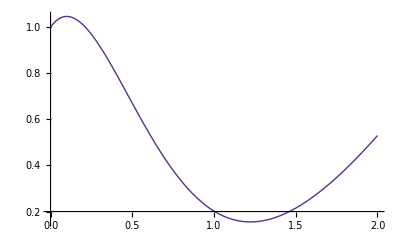

```mathematica
Plot[x[t],{t,0,2}]
```

```mathematica
Limit[ϕ[r],r->0]
```

(960+2258 ⅇ-960 ⅇ^2)/(-1+ⅇ^2)

```mathematica
%//N
```

0.686567

#### (b)

Writhe the ODE as two coupled first ordr ODES: v'(t)=2 t^2-8x(t)-4v(t), x'(t)=v(t). Combine them into a first order vector ODE,
z(t)={x(t),v(t)}, z'(t)=F(t) where F(t)={v(t),2 t^2-8x(t)-4v(t)}. Now use Euler’s method.

```mathematica
Clear[x,z]
```

```mathematica
F[{x_,v_},t_] = {v,2t^2-8x-4v};
```

```mathematica
z[0]={1,1};
z[n_] := z[n] = z[n-1] + Δt F[z[n-1],(n-1) Δt];
```

```mathematica
Δt = 0.01;
```

```mathematica
z[1]
```

{1.01,0.88}

```mathematica
Table[{n Δt,z[n][[1]]},{n,0,200}]
```

{{0.,1},{0.01,1.01},{0.02,1.0188},{0.03,1.02644},{0.04,1.03296},{0.05,1.0384},{0.06,1.04279},{0.07,1.04618},{0.08,1.0486},{0.09,1.05009},{0.1,1.05067},{0.11,1.0504},{0.12,1.0493},{0.13,1.04741},{0.14,1.04475},{0.15,1.04137},{0.16,1.03729},{0.17,1.03254},{0.18,1.02716},{0.19,1.02118},{0.2,1.01462},{0.21,1.00751},{0.22,0.999881},{0.23,0.991761},{0.24,0.983176},{0.25,0.974151},{0.26,0.964713},{0.27,0.954885},{0.28,0.944692},{0.29,0.934157},{0.3,0.923304},{0.31,0.912154},{0.32,0.90073},{0.33,0.889052},{0.34,0.877141},{0.35,0.865017},{0.36,0.852699},{0.37,0.840207},{0.38,0.827558},{0.39,0.81477},{0.4,0.801861},{0.41,0.788846},{0.42,0.775743},{0.43,0.762566},{0.44,0.749331},{0.45,0.736053},{0.46,0.722745},{0.47,0.70942},{0.48,0.696093},{0.49,0.682776},{0.5,0.66948},{0.51,0.656219},{0.52,0.643002},{0.53,0.62984},{0.54,0.616745},{0.55,0.603726},{0.56,0.590793},{0.57,0.577954},{0.58,0.56522},{0.59,0.552597},{0.6,0.540094},{0.61,0.527719},{0.62,0.515478},{0.63,0.50338},{0.64,0.49143},{0.65,0.479635},{0.66,0.468},{0.67,0.456532},{0.68,0.445235},{0.69,0.434114},{0.7,0.423175},{0.71,0.412421},{0.72,0.401856},{0.73,0.391485},{0.74,0.381311},{0.75,0.371338},{0.76,0.361568},{0.77,0.352004},{0.78,0.342649},{0.79,0.333505},{0.8,0.324574},{0.81,0.315859},{0.82,0.307361},{0.83,0.299081},{0.84,0.291021},{0.85,0.283181},{0.86,0.275564},{0.87,0.268169},{0.88,0.260998},{0.89,0.25405},{0.9,0.247327},{0.91,0.240827},{0.92,0.234551},{0.93,0.2285},{0.94,0.222672},{0.95,0.217068},{0.96,0.211686},{0.97,0.206526},{0.98,0.201588},{0.99,0.19687},{1.,0.192372},{1.01,0.188092},{1.02,0.18403},{1.03,0.180183},{1.04,0.176551},{1.05,0.173133},{1.06,0.169926},{1.07,0.16693},{1.08,0.164142},{1.09,0.161561},{1.1,0.159186},{1.11,0.157014},{1.12,0.155043},{1.13,0.153272},{1.14,0.151699},{1.15,0.150321},{1.16,0.149137},{1.17,0.148145},{1.18,0.147342},{1.19,0.146726},{1.2,0.146296},{1.21,0.146049},{1.22,0.145982},{1.23,0.146095},{1.24,0.146383},{1.25,0.146846},{1.26,0.147481},{1.27,0.148285},{1.28,0.149257},{1.29,0.150394},{1.3,0.151693},{1.31,0.153154},{1.32,0.154772},{1.33,0.156546},{1.34,0.158474},{1.35,0.160554},{1.36,0.162782},{1.37,0.165158},{1.38,0.167678},{1.39,0.170341},{1.4,0.173144},{1.41,0.176084},{1.42,0.179161},{1.43,0.182372},{1.44,0.185714},{1.45,0.189185},{1.46,0.192784},{1.47,0.196508},{1.48,0.200355},{1.49,0.204323},{1.5,0.20841},{1.51,0.212614},{1.52,0.216933},{1.53,0.221366},{1.54,0.22591},{1.55,0.230563},{1.56,0.235323},{1.57,0.24019},{1.58,0.245159},{1.59,0.250232},{1.6,0.255404},{1.61,0.260675},{1.62,0.266042},{1.63,0.271505},{1.64,0.277062},{1.65,0.28271},{1.66,0.288448},{1.67,0.294276},{1.68,0.300191},{1.69,0.306191},{1.7,0.312276},{1.71,0.318444},{1.72,0.324693},{1.73,0.331022},{1.74,0.33743},{1.75,0.343915},{1.76,0.350477},{1.77,0.357113},{1.78,0.363823},{1.79,0.370606},{1.8,0.37746},{1.81,0.384384},{1.82,0.391377},{1.83,0.398439},{1.84,0.405567},{1.85,0.412761},{1.86,0.42002},{1.87,0.427343},{1.88,0.434728},{1.89,0.442176},{1.9,0.449685},{1.91,0.457255},{1.92,0.464884},{1.93,0.472571},{1.94,0.480317},{1.95,0.488119},{1.96,0.495978},{1.97,0.503893},{1.98,0.511862},{1.99,0.519886},{2.,0.527963}}

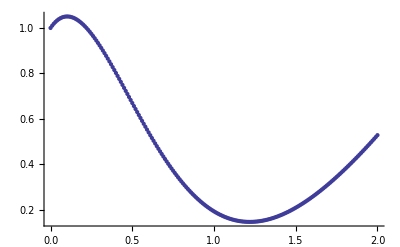

```mathematica
ListPlot[%]
```